## Setting Up Equations

```mathematica
<< KerrGeodesics`
<< GeneralRelativityTensors`
(*Clear["Global`*"]*)
KerrGeoSeparatrix[a,eC,χ]
```

KerrGeoEnergy::shdw: Symbol KerrGeoEnergy appears in multiple contexts {KerrGeodesics`ConstantsOfMotion`,Global`}; definitions in context KerrGeodesics`ConstantsOfMotion` may shadow or be shadowed by other definitions.

KerrGeoAngularMomentum::shdw: Symbol KerrGeoAngularMomentum appears in multiple contexts {KerrGeodesics`ConstantsOfMotion`,Global`}; definitions in context KerrGeodesics`ConstantsOfMotion` may shadow or be shadowed by other definitions.

KerrGeoCarterConstant::shdw: Symbol KerrGeoCarterConstant appears in multiple contexts {KerrGeodesics`ConstantsOfMotion`,Global`}; definitions in context KerrGeodesics`ConstantsOfMotion` may shadow or be shadowed by other definitions.

KerrGeoConstantsOfMotion::shdw: Symbol KerrGeoConstantsOfMotion appears in multiple contexts {KerrGeodesics`ConstantsOfMotion`,Global`}; definitions in context KerrGeodesics`ConstantsOfMotion` may shadow or be shadowed by other definitions.

KerrGeoISSO::shdw: Symbol KerrGeoISSO appears in multiple contexts {KerrGeodesics`SpecialOrbits`,Global`}; definitions in context KerrGeodesics`SpecialOrbits` may shadow or be shadowed by other definitions.

4.0714

```mathematica
ClearAll;
M = 1;

a = 0.9;

p =10.5;
eC =0.2;
Subscript[θ, inc]= π/4;

χ =Cos[Subscript[θ, inc]];

COM = KerrGeoConstantsOfMotion[a,p,eC,χ];
ϵ = COM["ℰ"];
L = COM["ℒ"];
Q = COM["𝒬"];

J = 1-ϵ^2;
RM = M- Sqrt[M^2-a^2];
RP = M+ Sqrt[M^2-a^2];

R1 = p/(1-eC)
R2 = p/(1+eC)
R3=1/J-(R1+R2)/2+Sqrt[((R1+R2)/2-1/(1-ϵ^2))^2-(a^2 Q)/(R1*R2*J)]
R4 =(a^2 Q)/(J*R1*R2*R3) 


Z1=Sqrt[1/2 (1+L^2/(a^2 (1-ϵ^2))+Q/(a^2 (1-ϵ^2))-√(-(4 Q)/(a^2 (1-ϵ^2))+(-1-L^2/(a^2 (1-ϵ^2))-Q/(a^2 (1-ϵ^2)))^2))];
Z2 =Sqrt[ (a^2(1-ϵ^2))/2 (1+L^2/(a^2 (1-ϵ^2))+Q/(a^2 (1-ϵ^2))+√(-(4 Q)/(a^2 (1-ϵ^2))+(-1-L^2/(a^2 (1-ϵ^2))-Q/(a^2 (1-ϵ^2)))^2))];
KZ = a^2*J(Z1^2/Z2^2);
KR = ((R3-R4)(R1-R2))/((R3-R1)(R4-R2));
R[r_] := -J(r-R1)(r-R2)(r-R3)(r-R4);

Plot[R[r], {r,0,3}];
hR = (R3-R4)/(R3-R1);
hP = hR(R1-RP)/(R4-RP);
hM =  hR(R1-RM)/(R4-RM);
```

13.125

8.75

1.46254

0.374134

### Radial Equation

0

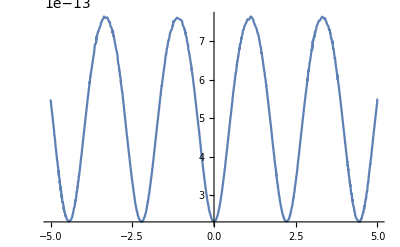

```mathematica
qR0 = 0
Subscript[Υ, r] = π/(2*EllipticK[KR])Sqrt[J(R3-R1)(R4-R2)];
qR[λ_]:= (Subscript[Υ, r] λ+ qR0);
r[λ_]:=(R1(R3-R4)(JacobiSN[EllipticK[KR]/π* (Subscript[Υ, r]*λ+ qR0),KR])^2-R4(R3-R1))/((R3-R4)(JacobiSN[EllipticK[KR]/π* (Subscript[Υ, r]*λ+qR0),KR])^2-(R3-R1));
Plot[(r'[λ])^2-RPoly1[r[λ]],{λ,-5,5}]
```

### Polar Equation

0

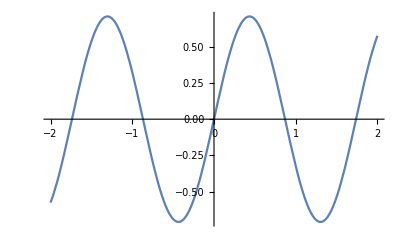

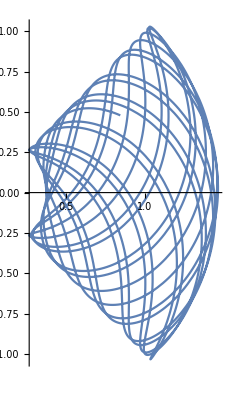

```mathematica
ΥZ = (π*Z2)/(2*EllipticK[KZ]);
qZ0 = 0

qZ[λ_]:= ΥZ*λ +qZ0
z[λ_] := Z1*JacobiSN[EllipticK[KZ]*2(ΥZ*λ+qZ0  )/π,KZ]  ;
θ[λ_] := ArcCos[Z1*JacobiSN[EllipticK[KZ]*2(ΥZ*λ + qZ0 )/π,KZ]];
PolyZ[λ_] := (z[λ]^2-Z1^2)*(a^2(1-ϵ^2)z[λ]^2-Z2^2)
Plot[z[λ],{λ,-2,2}]
ParametricPlot[{Re[r[λ]]*Cos[π/2-Re[θ[λ]]],Re[r[λ]]*Sin[π/2-Re[θ[λ]]]} , {λ,-5,20}, PlotRange->All]
```

### Azimuthal Part of Function

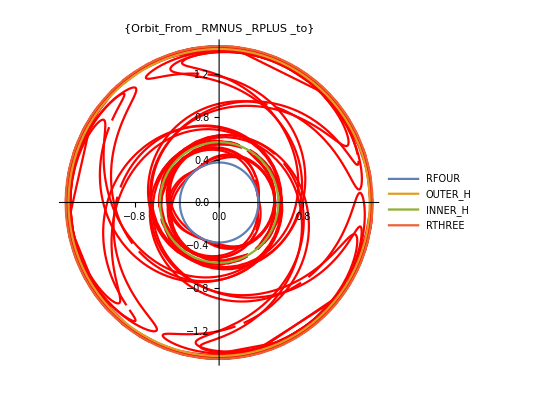

```mathematica
qϕ0 = 0;
Subscript[Υ, ϕr] = a/(RP-RM)((2ϵ*RP-a*L)/(R1-RP)(1-(R4-R1)/(R4-RP)(EllipticPi[hP,KR]/EllipticK[KR]) )- (2ϵ*RM-a*L)/(R1-RM)(1-(R4-R1)/(R4-RM)(EllipticPi[hM,KR]/EllipticK[KR]))  );
Subscript[Υ, ϕz]  = L/EllipticK[KZ] EllipticPi[Z1^2,KZ];
Subscript[Υ, ϕ]= Subscript[Υ, ϕr] +Subscript[Υ, ϕz];

qR[λ_]:= Subscript[Υ, r] λ+ qR0;
qZ[λ_]:= ΥZ*λ +qZ0;
qϕ[λ_]:= Subscript[Υ, ϕ]*λ + qϕ0;


ϕTr[ξ_]:= (-2*a*ϵ*(R4-R1))/((RP-RM)Sqrt[J*(R3-R1)(R4-R2)])*((2*RP-a*L/ϵ)/((R4-RP)(R1-RP))EllipticPi[hP,ξ,KR]-(2*RM-a*L/ϵ)/((R4-RM)(R1-RM))EllipticPi[hM,ξ,KR])
ϕTz[ξ_]:= -L/Z2 EllipticPi[Z1^2,ξ,KZ]

Subscript[ϕ, r][λ_] := ϕTr[JacobiAmplitude[EllipticK[KR]*qR[λ]/π,KR]] - ϕTr[π]/(2*π) qR[λ]
Subscript[ϕ, z][λ_]:= -ϕTz[JacobiAmplitude[EllipticK[KZ]*(2*qZ[λ])/π,KZ]] + ϕTz[π]/π qZ[λ]

ϕ[λ_]:= Subscript[ϕ, r][λ]+Subscript[ϕ, z][λ] + qϕ[λ]




Q1 = ParametricPlot[{Re[r[λ]]*Cos[Re[ϕ[λ+0.01*I]]],Re[r[λ]]*Sin[Re[ϕ[λ+0.01*I]]]}, {λ,0,20}, PlotRange->All, PlotLabel->{Orbit_From_RPLUS_to_RMNUS}, PlotStyle->Red, PlotLegends->ORBIT];
Q2 = ParametricPlot[{{R4*Cos[u],R4 *Sin[u]},
{RP*Cos[u],RP Sin[u]},
{RM*Cos[u],RM Sin[u]},
{R3*Cos[u],R3 Sin[u]}},{u,-π,π},MaxRecursion->1,PlotRange->All,PlotLegends->{RFOUR,OUTER_H,INNER_H,RTHREE}];

Show[Q1,Q2]
```

```mathematica
P1 = ParametricPlot3D[{Re[r[λ]]*Sin[Re[ϕ[λ+0.01*I]]]*Sin[Re[θ[λ+0.01*I]]],Re[r[λ]]*Sin[Re[θ[λ+0.01*I]]]*Cos[Re[ϕ[λ+0.01*I]]],Re[r[λ]]*Cos[Re[θ[λ+0.01*I]]]},{λ,0,20}, PlotStyle->Red,PlotRange->All];
P2 =ParametricPlot3D[{RP*Sin[u] Sin[v],RP*Cos[u] Sin[v],RP*Cos[v]},{u,-π,π},{v,-π,π},MaxRecursion->4,PlotStyle->{Opacity[1.0],Black,Specularity[White,10]}, Lighting->"Neutral",Axes->None,Mesh->None,PlotRange->All];
Show[P1,P2]
```

-Graphics3D-

### Time Function

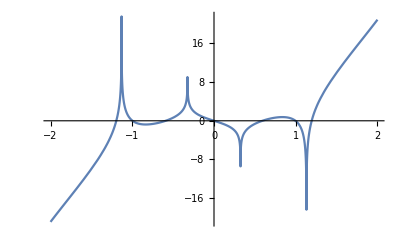

```mathematica
qT0 = 0;
Subscript[Υ, Tr] = (4+a^2)ϵ+ϵ(1/2((4+R3+R4+R1)R1-R3*R4+(R3-R1)(R4-R2)EllipticE[KR]/EllipticK[KR]+(4+R3+R4+R1+R2)(R4-R1)EllipticPi[hR,KR]/EllipticK[KR])+2/(RP-RM)(((4-a*L/ϵ)RP-2*a^2)/(R1-RP)(1-(R4-R1)/(R4-RP)EllipticPi[hP,KR]/EllipticK[KR])-((4-a*L/ϵ)RM-2*a^2)/(R1-RM)(1-(R4-R1)/(R4-RM)EllipticPi[hM,KR]/EllipticK[KR])));
Subscript[Υ, Tz] = -a^2*ϵ+(ϵ*Q)/(J(Z1^2))(1-EllipticE[KZ]/EllipticK[KZ]);
Subscript[Υ, T]= Subscript[Υ, Tr] +Subscript[Υ, Tz];
qT[λ_]:= Subscript[Υ, T]*λ+qT0

TTr[ξ_]:= (ϵ(R4-R1))/Sqrt[J(R3-R1)(R4-R2)]((4+R3+R4+R1+R2)EllipticPi[hR,ξ,KR]-4/(RP-RM)((RP(4-a*L/ϵ)-2*a^2)/((R4-RP)(R1-RP))EllipticPi[hP,ξ,KR]-(RM(4-a*L/ϵ)-2*a^2)/((R4-RM)(R1-RM))EllipticPi[hM,ξ,KR])+((R3-R1)(R4-R2))/(R4-R1)(EllipticE[ξ,KR]-(hR*Sin[ξ]*Cos[ξ]Sqrt[1-KR*(Sin[ξ])^2])/(1-hR*(Sin[ξ])^2)))
TTz[ξ_]:= -ϵ/J Z2*EllipticE[ξ,KZ]

Subscript[T, r][λ_] := TTr[JacobiAmplitude[EllipticK[KR]*qR[λ]/π,KR]] - TTr[π]/(2*π) qR[λ]
Subscript[T, z][λ_]:= TTz[JacobiAmplitude[EllipticK[KZ]*(2*qZ[λ])/π,KZ]] - TTz[π]/π qZ[λ]

T[λ_]:= Subscript[T, r][λ]+Subscript[T, z][λ] + qT[λ]
Plot[T[λ],{λ,-2,2}]
```

### Mino Time in terms of Proper Time

```mathematica
Simplify[Integrate[r^2/(Sqrt[J](R1-r)^(1/2)(R2-R)^(1/2)(R3-R)^(1/2)(r-R4)^(1/2)), r]];
qτ0=0;

Subscript[Υ, τ,r] = ((R3+R4+R1)*R1-R3*R4)/2+(R3-R1)(R4-R2)EllipticE[KR]/(2*EllipticK[KR])+(R1+R2+R3+R4)(R4-R1)EllipticPi[hR,KR]/(2*EllipticK[KR]);
Subscript[Υ, τ,z] = Z2^2/J(1-EllipticE[KZ]/EllipticK[KZ]);
Subscript[Υ, τ] =  Subscript[Υ, τ,r]+ Subscript[Υ, τ,z]
qτ[λ_]:= Subscript[Υ, τ]*λ+qτ0
```

1.6972

```mathematica
Subscript[τT, r][ξ_] :=1/Sqrt[J*(R3-R1)(R4-R2)](((R3+R4+R1)R1-R3*R4)EllipticF[ξ,KR]+(R3-R1)(R4-R2)EllipticE[ξ,KR]+(R4-R1)(R3+R4+R1+R2)EllipticPi[hR,ξ,KR]-(hR(R3-R1)(R4-R2)Sin[ξ]Cos[ξ]Sqrt[1-KR*(Sin[ξ])^2])/(1-hR*(Sin[ξ])^2));

Subscript[τT, z][ξ_] :=(Z2  (EllipticF[ξ,KZ]-EllipticE[ ξ,KZ]))/J ;
Subscript[τ, z][λ_]:= Subscript[τT, z][JacobiAmplitude[EllipticK[KZ]*2 qZ[λ]/π,KZ]] - (Subscript[τT, z][π])/π qZ[λ];
Subscript[τ, r][λ_]:=Subscript[τT, r][JacobiAmplitude[EllipticK[KR]*qR[λ]/π,KR]] - (Subscript[τT, r][π])/(2*π)qR[λ];


τ[λ_]:= Subscript[τ, z][λ]+Subscript[τ, r][λ]+qτ[λ]
```

### Small Q approximation

```mathematica
RIQ[Q_] :=Sqrt[ (-4-a^2-Q+a^2 ϵ^2-√(12 a^2 Q (-3+3 ϵ^2)+(4+a^2+Q-a^2 ϵ^2)^2))/(6 (-1+ϵ^2))]
```

### Kruskal Coordinates

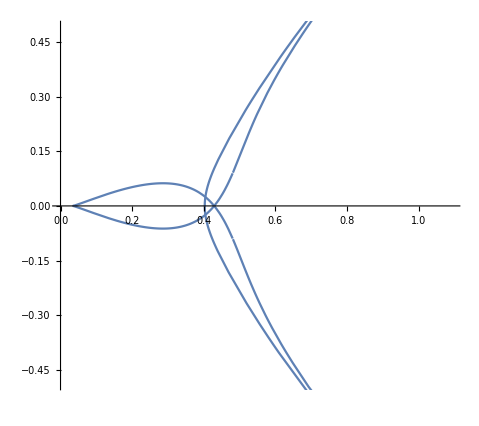

```mathematica
σP = (M*RP)/Sqrt[M^2-a^2];
σM = (M*RM)/Sqrt[M^2-a^2];
ν = σM/σP;


V[λ_] := Abs[r[λ]-RP]^(1/2)/Abs[r[λ]-RM]^(ν/2)Exp[(r[λ]+T[λ])/(2 σP)];
U[λ_] := -Abs[r[λ]-RP]^(1/2)/Abs[r[λ]-RM]^(ν/2)Exp[(r[λ]-T[λ])/(2 σP)];

TR[λ_]:= (r[λ]/RP-1)^(1/2 E^(r[λ]/RP))Sinh[T[λ]/(2*RP)]
X[λ_]:= (r[λ]/RP-1)^(1/2 E^(r[λ]/RP))Cosh[T[λ]/(2*RP)]
ParametricPlot[{Re[-X[λ]],Re[TR[λ]]},{λ,-1,1}]
```

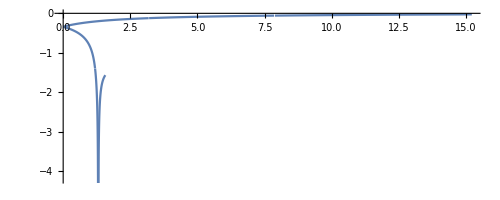

```mathematica
ParametricPlot[{Re[V[λ]],Re[U[λ]]},{λ,0,2}]
```

### Analysis

```mathematica
(*ListX = Range[20,200,0.01];

ListKP = θ''/@ListX;
Listθ = ϕ''/@ListX;

ListPlot[{Transpose[{ListX,ListKP}], Transpose[{ListX,Listθ}]}, Joined->True,PlotLegends->Automatic]

(*FourListKP = Re[Fourier[ListKP]];
FourListθ = Re[Fourier[Listθ]];

ListPlot[{Transpose[{ListX,FourListKP}],Transpose[{ListX,FourListθ}]}, Joined->True,PlotRange->{{20,200},{-0.11,.1}},PlotLegends->Automatic]*)


fB=1.0;
Data1=Table[ϕ''[x],{x,1900,2000,1/10}];
sra=10./1;
inco=sra/Length[Data1];
fresa=Table[f,{f,0,sra-inco,inco}];
fData=Transpose[{fresa,Flatten[Abs[Fourier[Data1]]]}];
peaks=fData[[FindPeaks[fData[[All,2]]][[All,1]]]];
ListPlot[fData,PlotRange->{Full,Full},Joined->True,Frame->True,FrameLabel->{Row[{Style["Frequency",FontSlant->Italic,FontSize->15]}],Row[{Style["Amplitude",FontSlant->Italic,FontSize->15]}]},LabelStyle->Blue,FrameTicksStyle->Directive[Orange,15],ImageSize->900,PlotStyle->{Red},Joined->True,AspectRatio->0.5,Epilog->{PointSize[0.003],Point[fData],Black,PointSize[.01],Point[peaks]},PlotLabel->"Peaks: "<>ToString[peaks]]

fB=1.0;
Data1=Table[θ''[x],{x,1900,2000,1/10}];
sra=10./1;
inco=sra/Length[Data1];
fresa=Table[f,{f,0,sra-inco,inco}];
fData=Transpose[{fresa,Flatten[Abs[Fourier[Data1]]]}];
peaks=fData[[FindPeaks[fData[[All,2]]][[All,1]]]];
ListPlot[fData,PlotRange->{Full,Full},Joined->True,Frame->True,FrameLabel->{Row[{Style["Frequency",FontSlant->Italic,FontSize->15]}],Row[{Style["Amplitude",FontSlant->Italic,FontSize->15]}]},LabelStyle->Blue,FrameTicksStyle->Directive[Orange,15],ImageSize->900,PlotStyle->{Red},Joined->True,AspectRatio->0.5,Epilog->{PointSize[0.003],Point[fData],Black,PointSize[.01],Point[peaks]},PlotLabel->"Peaks: "<>ToString[peaks]]*)
```

-0.29749

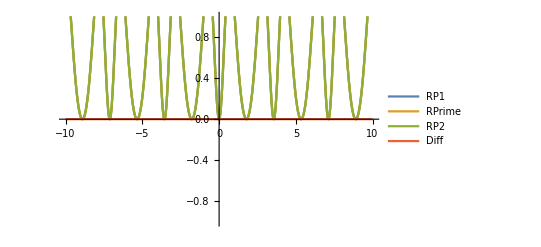

```mathematica
RPoly1[r_]:= (ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q)

RPoly2[r_]:=-J(R1-r)(R2-r)(R3-r)(R4-r)
r'[2]

Polyphir[r_]:= (a(ϵ(r^2+a^2)-a*L))/((r-RM)(r-RP));
Plot[{RPoly1[r[λ]], (r'[λ])^2, RPoly2[r[λ]], (r'[λ])^2- RPoly1[r[λ]]},{λ,-10,10}, PlotLegends->{RP1,RPrime,RP2,Diff}, PlotRange->{{-10,10},{-1,1}}]
```

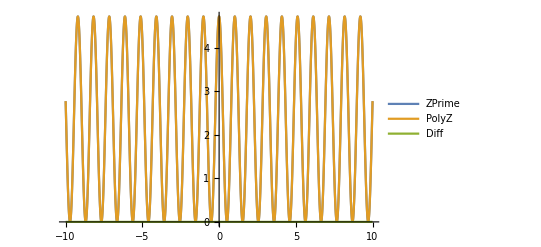

```mathematica
PolyZ[λ_] := (z[λ]^2-Z1^2)*(a^2(1-ϵ^2)z[λ]^2-Z2^2)
Plot[{(z'[λ])^2, PolyZ[λ], (z'[λ])^2- PolyZ[λ]}, {λ,-10,10},PlotRange->All, PlotLegends->{ZPrime,PolyZ,Diff}]
```

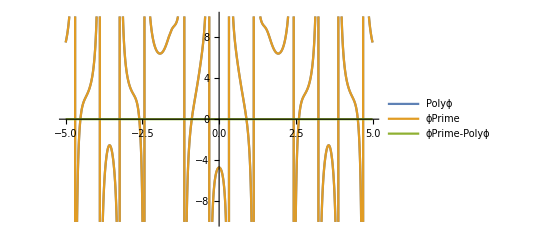

```mathematica
(*Plot[Im[ϕ[λ]],{λ,-5,5}]*)
Polyϕ[λ_]:= a/((r[λ]-RP)(r[λ]-RM))(ϵ(r[λ]^2+a^2)-a*L) + L/(1-z[λ]^2)-a*ϵ
Plot[{Polyϕ[λ],Re[ϕ'[λ]],Re[ϕ'[λ]]-Polyϕ[λ]},{λ,-5,5}, PlotRange->{{-5,5},{-10,10}},PlotLegends->{Polyϕ,ϕPrime,ϕPrime-Polyϕ}]
```

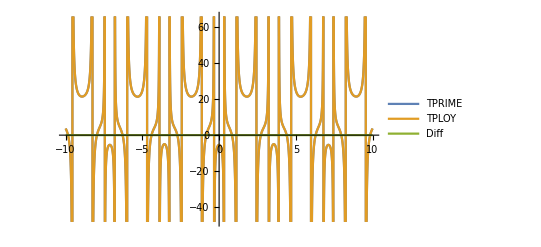

```mathematica
TPoly[λ_]:=  (r[λ]^2+a^2)/((r[λ]-RP)(r[λ]-RM))(ϵ(r[λ]^2+a^2)-a*L)-a^2 ϵ(1-z[λ]^2)+a*L
Plot[{Re[T'[λ]],TPoly[λ],Re[T'[λ]]-TPoly[λ] },{λ,-10,10},PlotLegends->{TPRIME,TPLOY,Diff}]
```

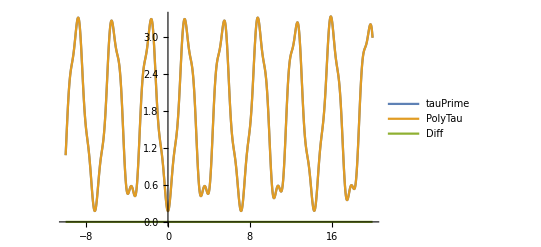

```mathematica
Plot[{τ'[λ],r[λ]^2+a^2 z[λ]^2,τ'[λ]-(r[λ]^2+a^2 z[λ]^2)},{λ,-10,20},PlotRange->All,{PlotLegends->{tauPrime,PolyTau,Diff}}]
```